#### Preamble

```mathematica
SetDirectory[NotebookDirectory[]]
<<"MaTeX`"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Nano_CSM_SDistAll.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Nano_CSM_Biosensor.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"

fs = 9;
texStyle:={FontFamily->"Latin Modern Roman",FontSize->fs,Black};
graphsOpts:= {Mesh-> Full,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> ColorData[3]}
SetOptions[ListLinePlot,graphsOpts];
```

/home/juanathan/Documentos/Wolfram Mathematica/Wolfram_scripts

#### Common Parameters

```mathematica
ang = Range[0,90,1.]*Pi/180.;
lda = {550., 600., 650};

rad = 30.;
cfrac = .3;
(*To recover fresnel*)
ind = Transpose[{1.,1.,1.5}&/@ lda]; (*nMatrix, nParticles, nSubstrate*)
(*Au NPs with no size correction*)
indAu = Transpose[{1.,JohnsonChristyAuRef[#],1.5}&/@ lda]; (*nMatrix, nParticles, nSubstrate*)
ind1 = Transpose[{1., 1.} & /@ lda];
ind2 = Transpose[{1., 1.5} & /@ lda];
```

```mathematica
wlen = Range[530,535];
radius = Range[10,11];
ni = ConstantArray[2,Length[wlen]];
JohnsonChristyAuRefSize[wlen,radius]
JohnsonChristyAuRefSize[wlen,radius]/ni
```

{{0.649376+2.21999 ⅈ,0.638837+2.21854 ⅈ},{0.64186+2.23328 ⅈ,0.631304+2.23188 ⅈ},{0.634728+2.24654 ⅈ,0.624155+2.24519 ⅈ},{0.627955+2.25978 ⅈ,0.617366+2.25848 ⅈ},{0.621515+2.27299 ⅈ,0.610911+2.27173 ⅈ},{0.615386+2.28616 ⅈ,0.604767+2.28494 ⅈ}}

{{0.324688+1.11 ⅈ,0.319419+1.10927 ⅈ},{0.32093+1.11664 ⅈ,0.315652+1.11594 ⅈ},{0.317364+1.12327 ⅈ,0.312077+1.1226 ⅈ},{0.313977+1.12989 ⅈ,0.308683+1.12924 ⅈ},{0.310758+1.13649 ⅈ,0.305456+1.13587 ⅈ},{0.307693+1.14308 ⅈ,0.302384+1.14247 ⅈ}}

### Fresnel

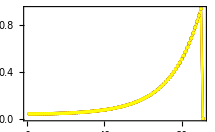
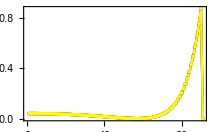
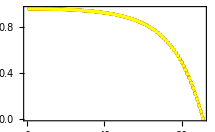
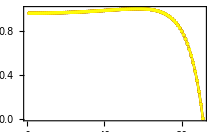

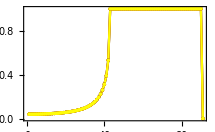
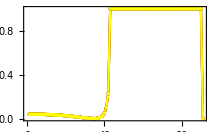
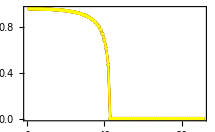
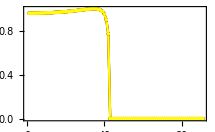

```mathematica
fresnel = Through[{fresnelRs, fresnelRp,fresnelTs,fresnelTp}[ang, toMap/@ind2]]; (*[[rt*pol, ang, lda*)
imp1 = CSMImpedance[ang,#]&/@{ind1, ind1, ind2, ind2};
fresnel= Transpose[fresnel,2<->3];
imp1 = Transpose[imp1, 2<->3];
frext = ListLinePlot[#,PlotRange->All]&/@(imp1*norm2[fresnel])

fresnel = Through[{fresnelRs, fresnelRp,fresnelTs,fresnelTp}[ang, toMap/@ Reverse@ind2]]; (*[[rt*pol, ang, lda*)
imp2 = CSMImpedance[ang,#]&/@{ind1, ind1,  Reverse@ind2,  Reverse@ind2};
fresnel= Transpose[fresnel,2<->3];
imp2 = Transpose[imp2, 2<->3];
frint = ListLinePlot[#,PlotRange->All]&/@(imp2*norm2[fresnel])
```

## Mono vs Polydisperse (Gold AuNP - LogNormal)

0.000289425

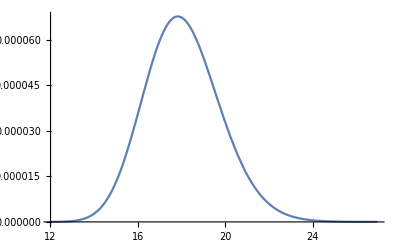

```mathematica
mu  = 18;(*Central value of the Radii Distribution*)
sigma =1.1;(*Standard deviation from Raddii Distribution*)

(*Upper and lower integration limits fo the polydispersed case*)
rhost = cfrac * Exp[-2*Log[sigma]^2]/(Pi * mu^2)
sizeDist = rhost * Exp[-(Log[#/#2]/(Sqrt[2.]*Log[#3]))^2] / (#*Sqrt[2.*Pi]*Log[#3])&;
Plot[sizeDist[x,mu,sigma],{x,mu*sigma^(-Sqrt[18.]),mu*sigma^(Sqrt[18.])},PlotRange->All]
```

```mathematica
indAu = Transpose[{1.,JohnsonChristyAuRef[#],1.5}&/@ lda]; (*nMatrix, nParticles, nSubstrate*)
```

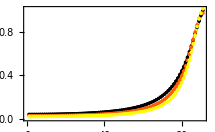
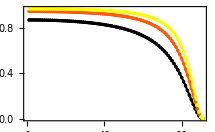

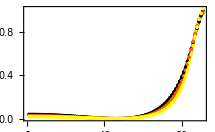
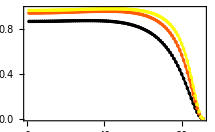

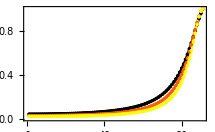
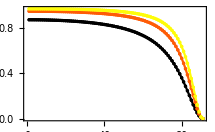

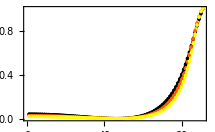
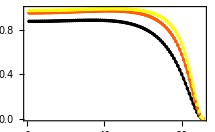

```mathematica
dataBio = CSMBioReflectionTransmission[ang, indAu[[1]],lda, cfrac, {mu, sigma}];
ListLinePlot[norm2[#],PlotRange->All]&/@Transpose[dataBio[[1]] ,2<->3]
ListLinePlot[norm2[#],PlotRange->All]&/@Transpose[dataBio[[2]] ,2<->3]

dataPoly = CSMPolyAmplitudeReflectionTransmission[ang, indAu[[;;2]],lda, cfrac, {mu, sigma}];
ListLinePlot[norm2[#],PlotRange->All]&/@Transpose[dataPoly[[1]] ,2<->3]
ListLinePlot[norm2[#],PlotRange->All]&/@Transpose[dataPoly[[2]] ,2<->3]
```

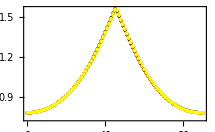
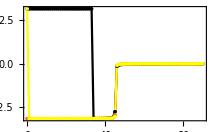

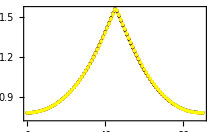
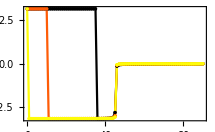

```mathematica
ListLinePlot[Transpose[#],DataRange->{0,90}, PlotRange->All]&/@ ({ArcTan[Abs[#]],Arg[#]}&@ (Divide@@dataBio[[;;,1]]))
ListLinePlot[Transpose[#],DataRange->{0,90}, PlotRange->All]&/@ ({ArcTan[Abs[#]],Arg[#]}&@ (Divide@@dataPoly[[;;,1]]))
```

```mathematica
indAu = Transpose[{1.,JohnsonChristyAuRef[#],1.5}&/@ lda]; (*nMatrix, nParticles, nSubstrate*)
```

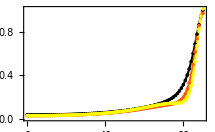
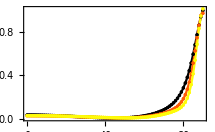

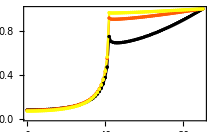
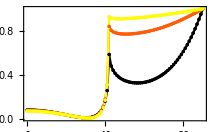

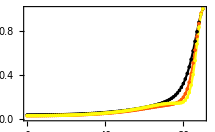
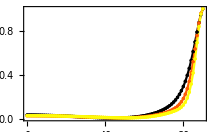

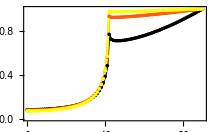
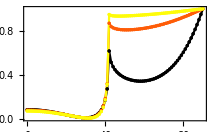

```mathematica
CSMBioReflectionExt[ang, indAu[[{1,3}]], lda, cfrac,{mu, sigma}] ;
ListLinePlot[Transpose[norm2[#]],DataRange->{0,90}, PlotRange->All]& /@ %

CSMBioReflectionInt[ang, indAu[[{1,3}]], lda, cfrac,{mu, sigma}] ;
ListLinePlot[Transpose[norm2[#]],DataRange->{0,90}, PlotRange->All]& /@ %

CSMPolyReflectionExt[ang, indAu, lda, cfrac,{mu, sigma}] ;
ListLinePlot[Transpose[norm2[#]],DataRange->{0,90}, PlotRange->All]& /@ %

CSMPolyReflectionInt[ang, indAu, lda, cfrac,{mu, sigma}] ;
ListLinePlot[Transpose[norm2[#]],DataRange->{0,90}, PlotRange->All]& /@ %
```

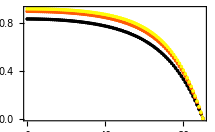
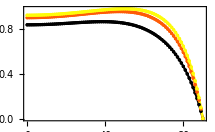

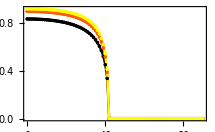
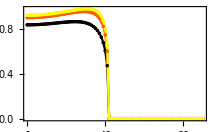

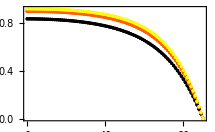
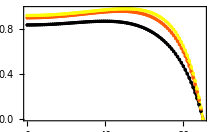

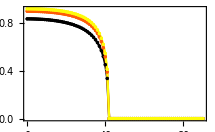
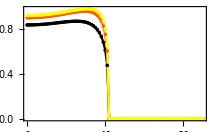

```mathematica
CSMBioTransmissionExt[ang, indAu[[{1,3}]], lda, cfrac,{mu, sigma}] ;
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ (Transpose[norm2[%],2<->3]*imp1[[{3,4}]])

CSMBioTransmissionInt[ang, indAu[[{1,3}]], lda, cfrac,{mu, sigma}] ;
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ (Transpose[norm2[%],2<->3]*imp2[[{3,4}]])

CSMPolyTransmissionExt[ang, indAu, lda, cfrac,{mu, sigma}] ;
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ (Transpose[norm2[%],2<->3]*imp1[[{3,4}]])

CSMPolyTransmissionInt[ang, indAu, lda, cfrac,{mu, sigma}] ;
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ (Transpose[norm2[%],2<->3]*imp2[[{3,4}]])
```

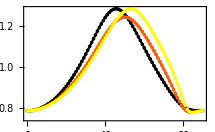
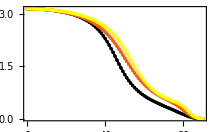

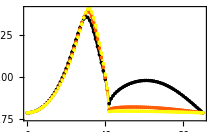
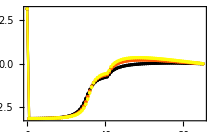

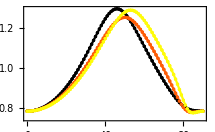
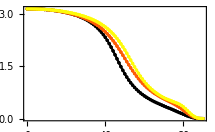

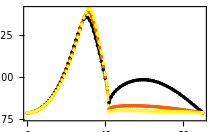
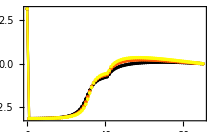

```mathematica
CSMPolyElipsometryExt[ang, indAu, lda, cfrac,{mu, sigma}] ;
ListLinePlot[Transpose@Abs@#,DataRange->{0,90}, PlotRange->All]& /@ %

CSMPolyElipsometryInt[ang, indAu, lda, cfrac,{mu, sigma}] ;
ListLinePlot[Transpose@#,DataRange->{0,90}, PlotRange->All]& /@ %

CSMBioElipsometryExt[ang, indAu[[{1,3}]], lda, cfrac,{mu, sigma}] ;
ListLinePlot[Transpose@Abs@#,DataRange->{0,90}, PlotRange->All]& /@ %

CSMBioElipsometryInt[ang, indAu[[{1,3}]], lda, cfrac,{mu, sigma}] ;
ListLinePlot[Transpose@#,DataRange->{0,90}, PlotRange->All]& /@ %
```

## Mono vs Polydisperse (Gold AuNP -Normal)

PDF[NormalDistribution[mu,sigma],#1]&

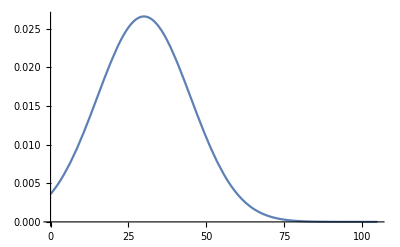

```mathematica
mu  = 30;(*Central value of the Radii Distribution*)
sigma =30*.5;(*Standard deviation from Raddii Distribution*)
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Nano_CSM_SDistAll.wls"

sizeDist1 = PDF[NormalDistribution[mu,sigma],#]&
Plot[sizeDist1[x],{x,If[#<=0,0,#]&[mu-5*sigma],mu+5*sigma},PlotRange->All]
```

```mathematica
indAu = Transpose[{1.,JohnsonChristyAuRef[#],1.5}&/@ lda]; (*nMatrix, nParticles, nSubstrate*)
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

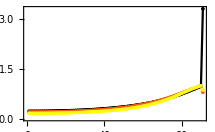
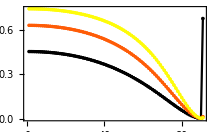

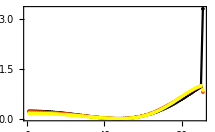
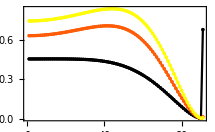

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

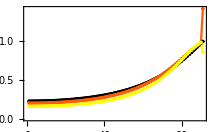
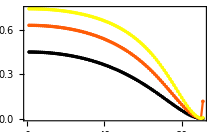

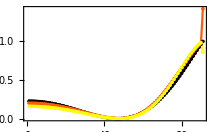
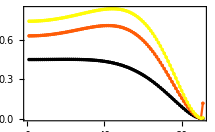

```mathematica
dataBio = CSMBioReflectionTransmission[ang, indAu[[1]],lda, cfrac, {mu, sigma}, "SizeDistribution"->"Normal"];
ListLinePlot[norm2[#],PlotRange->All]&/@Transpose[dataBio[[1]] ,2<->3]
ListLinePlot[norm2[#],PlotRange->All]&/@Transpose[dataBio[[2]] ,2<->3]

dataPoly = CSMPolyAmplitudeReflectionTransmission[ang, indAu[[;;2]],lda, cfrac, {mu, sigma}, "SizeDistribution"->"Normal"];
ListLinePlot[norm2[#],PlotRange->All]&/@Transpose[dataPoly[[1]] ,2<->3]
ListLinePlot[norm2[#],PlotRange->All]&/@Transpose[dataPoly[[2]] ,2<->3]
```

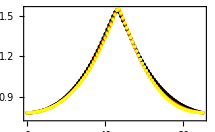
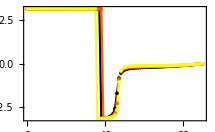

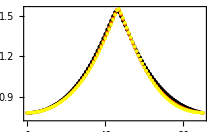
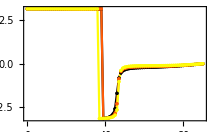

```mathematica
ListLinePlot[Transpose[#],DataRange->{0,90}, PlotRange->All]&/@ ({ArcTan[Abs[#]],Arg[#]}&@ (Divide@@dataBio[[;;,1]]))
ListLinePlot[Transpose[#],DataRange->{0,90}, PlotRange->All]&/@ ({ArcTan[Abs[#]],Arg[#]}&@ (Divide@@dataPoly[[;;,1]]))
```

```mathematica
indAu = Transpose[{1.,JohnsonChristyAuRef[#],1.5}&/@ lda]; (*nMatrix, nParticles, nSubstrate*)
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

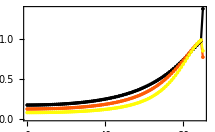
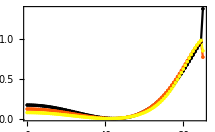

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

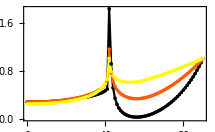
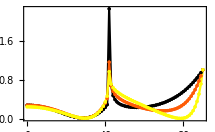

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

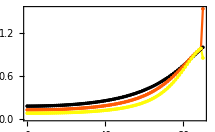
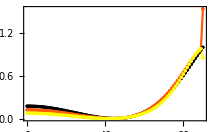

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

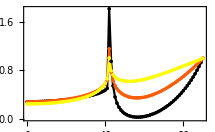
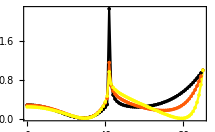

```mathematica
CSMBioReflectionExt[ang, indAu[[{1,3}]], lda, cfrac,{mu, sigma}, "SizeDistribution"->"Normal"] ;
ListLinePlot[Transpose[norm2[#]],DataRange->{0,90}, PlotRange->All]& /@ %

CSMBioReflectionInt[ang, indAu[[{1,3}]], lda, cfrac,{mu, sigma}, "SizeDistribution"->"Normal"] ;
ListLinePlot[Transpose[norm2[#]],DataRange->{0,90}, PlotRange->All]& /@ %

CSMPolyReflectionExt[ang, indAu, lda, cfrac,{mu, sigma}, "SizeDistribution"->"Normal"] ;
ListLinePlot[Transpose[norm2[#]],DataRange->{0,90}, PlotRange->All]& /@ %

CSMPolyReflectionInt[ang, indAu, lda, cfrac,{mu, sigma}, "SizeDistribution"->"Normal"] ;
ListLinePlot[Transpose[norm2[#]],DataRange->{0,90}, PlotRange->All]& /@ %
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

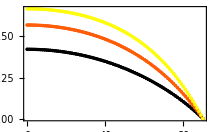
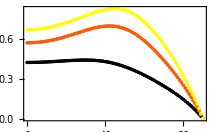

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

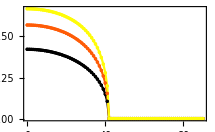
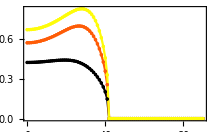

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

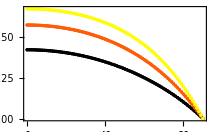
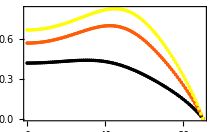

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

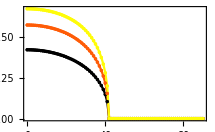
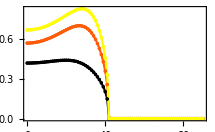

```mathematica
CSMBioTransmissionExt[ang, indAu[[{1,3}]], lda, cfrac,{mu, sigma}, "SizeDistribution"->"Normal"] ;
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ (Transpose[norm2[%],2<->3]*imp1[[{3,4}]])

CSMBioTransmissionInt[ang, indAu[[{1,3}]], lda, cfrac,{mu, sigma}, "SizeDistribution"->"Normal"] ;
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ (Transpose[norm2[%],2<->3]*imp2[[{3,4}]])

CSMPolyTransmissionExt[ang, indAu, lda, cfrac,{mu, sigma}, "SizeDistribution"->"Normal"] ;
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ (Transpose[norm2[%],2<->3]*imp1[[{3,4}]])

CSMPolyTransmissionInt[ang, indAu, lda, cfrac,{mu, sigma}, "SizeDistribution"->"Normal"] ;
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ (Transpose[norm2[%],2<->3]*imp2[[{3,4}]])
```

```mathematica
"SizeDistribution"->"Normal"
CSMPolyElipsometryExt[ang, indAu, lda, cfrac,{mu, sigma}, "SizeDistribution"->"Normal"] ;
ListLinePlot[Transpose@Abs@#,DataRange->{0,90}, PlotRange->All]& /@ %

CSMPolyElipsometryInt[ang, indAu, lda, cfrac,{mu, sigma}, "SizeDistribution"->"Normal"] ;
ListLinePlot[Transpose@#,DataRange->{0,90}, PlotRange->All]& /@ %

CSMBioElipsometryExt[ang, indAu[[{1,3}]], lda, cfrac,{mu, sigma}, "SizeDistribution"->"Normal"] ;
ListLinePlot[Transpose@Abs@#,DataRange->{0,90}, PlotRange->All]& /@ %

CSMBioElipsometryInt[ang, indAu[[{1,3}]], lda, cfrac,{mu, sigma}, "SizeDistribution"->"Normal"] ;
ListLinePlot[Transpose@#,DataRange->{0,90}, PlotRange->All]& /@ %
```

SizeDistribution→Normal

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

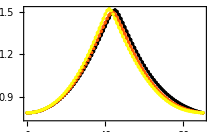
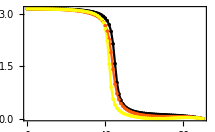

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

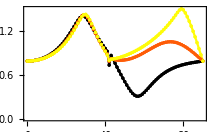
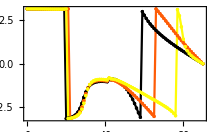

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

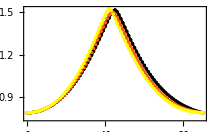
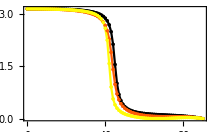

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

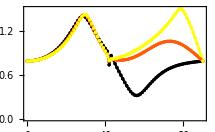
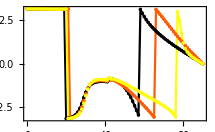

```mathematica
ListLinePlot[norm2[#],PlotRange->All]&/@Transpose[dataPoly[[2]] ,2<->3]
```